```mathematica
f[x_]:=x^2 Cos[x];
window={{.5,2},{-2,2}};
bisectleft=window[[1,1]];
bisectright=window[[1,2]];
bisectpoints={};
bisectcount=0;
newtonguess=1.3;
newtongraphs={};
newtonpoints={};
newtoncount=0;
```

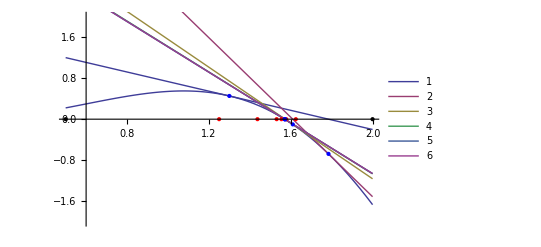

0.0161088 Bisection absolute error after 6 iterations 
0. Newton absolute error after 6 iterations

```mathematica
bisectcount++;
bisectguess=(bisectleft+bisectright)/2;
If[f[bisectleft]*f[bisectguess]>0,bisectleft=bisectguess,bisectright=bisectguess];
bisectpoints=Append[bisectpoints,{bisectguess,0}];

newtoncount++;
newtonpoints=Append[newtonpoints,{newtonguess,f[newtonguess]}];
newtongraphs=Append[newtongraphs,f[newtonguess]+f'[newtonguess](x-newtonguess)];
newtonguess=newtonguess-f[newtonguess]/f'[newtonguess];

Show[Plot[f[x],{x,window[[1,1]],window[[1,2]]},PlotRange->window[[2]],ImageSize->Full],Plot[newtongraphs,{x,window[[1,1]],window[[1,2]]},PlotLegends->Placed[Automatic,Below]],ListPlot[bisectpoints,PlotStyle->{Red,PointSize[Large]}],ListPlot[newtonpoints,PlotStyle->{Blue,PointSize[Large]}],ListPlot[{{window[[1,1]],0},{window[[1,2]],0}},PlotStyle->{Black,PointSize[Large]}]]
StringForm["`1` Bisection absolute error after `3` iterations \n`2` Newton absolute error after `4` iterations",N[Abs[bisectguess-π/2]],Abs[newtonguess-π/2],bisectcount,newtoncount]
```